```mathematica
Solve[{D[v0+b1^2*v1+b2^2*v2-2b1*cv1-2b2*cv2-2b1*b2*cv12,b1]==0,D[v0+b1^2*v1+b2^2*v2-2b1*cv1-2b2*cv2-2b1*b2*cv12,b2]==0},{b1,b2}]//FullSimplify
```

{{b1→(cv12 cv2+cv1 v2)/(-cv12^2+v1 v2),b2→(cv1 cv12+cv2 v1)/(-cv12^2+v1 v2)}}

```mathematica
Solve[{D[v0+b1^2*v1+b2^2*v2+b3^2*v3-2b1*cv1-2b2*cv2-2b3*cv3-2b1*b2*cv12-2b1*b3*cv13-2b2*b3*cv23,b1]==0,D[v0+b1^2*v1+b2^2*v2+b3^2*v3-2b1*cv1-2b2*cv2-2b3*cv3-2b1*b2*cv12-2b1*b3*cv13-2b2*b3*cv23,b2]==0,D[v0+b1^2*v1+b2^2*v2+b3^2*v3-2b1*cv1-2b2*cv2-2b3*cv3-2b1*b2*cv12-2b1*b3*cv13-2b2*b3*cv23,b3]==0},{b1,b2,b3}]
```

{{b1→-(cv13 cv2 cv23-cv1 cv23^2+cv12 cv23 cv3+cv13 cv3 v2+cv12 cv2 v3+cv1 v2 v3)/(2 cv12 cv13 cv23+cv23^2 v1+cv13^2 v2+cv12^2 v3-v1 v2 v3),b2→-(-cv13^2 cv2+cv1 cv13 cv23+cv12 cv13 cv3+cv23 cv3 v1+cv1 cv12 v3+cv2 v1 v3)/(2 cv12 cv13 cv23+cv23^2 v1+cv13^2 v2+cv12^2 v3-v1 v2 v3),b3→-(cv12 cv13 cv2+cv1 cv12 cv23-cv12^2 cv3+cv2 cv23 v1+cv1 cv13 v2+cv3 v1 v2)/(2 cv12 cv13 cv23+cv23^2 v1+cv13^2 v2+cv12^2 v3-v1 v2 v3)}}

```mathematica
(c1-theta1)^2(c2-theta2)^2//ExpandAll
```

c1^2 c2^2-2 c1 c2^2 theta1+c2^2 theta1^2-2 c1^2 c2 theta2+4 c1 c2 theta1 theta2-2 c2 theta1^2 theta2+c1^2 theta2^2-2 c1 theta1 theta2^2+theta1^2 theta2^2

```mathematica
(c1-theta
```

```mathematica
Solve[D[x^2(4-2x)^2/9,x]==0,x]
```

{{x→0},{x→1},{x→2}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
Solve[{2x y^2==lambda 2,2 x^2 y==-3lambda,2x-3y==4},{x,y,lambda}]
```

{{x→0,y→-4/3,lambda→0},{x→1,y→-2/3,lambda→4/9},{x→2,y→0,lambda→0}}

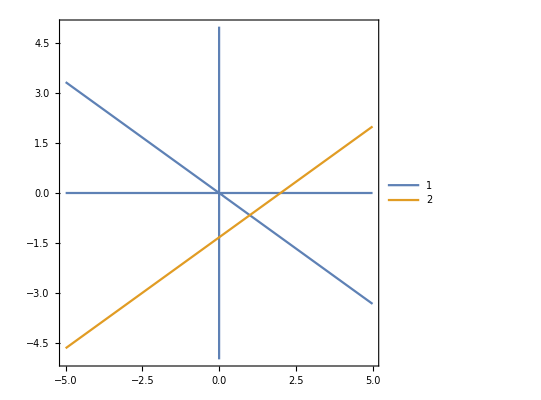

```mathematica
ContourPlot[{(2x y^2)/2==(2 x^2 y)/-3,2x-3y==4},{x,-5,5},{y,-5,5},PlotLegends->Automatic,MaxRecursion->4]
```